```mathematica
Clear["Global`*"]
BasisFunc[n_]:=Function[{x},Sqrt[(2n+1)/2]LegendreP[n,x]]
BasisMax=10;

qFunc[x_]=PDF[NormalDistribution[0.1,0.2],x];

(*Plot[Evaluate[Table[BasisFunc[n][x],{n,0,BasisMax}]],{x,-1,1}]*)
```

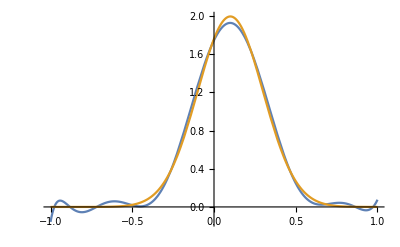

{0.,0.,4.7434,2.80614,-10.3418,-7.51151,11.405,10.1708,-8.32927,-9.23168,4.4613}

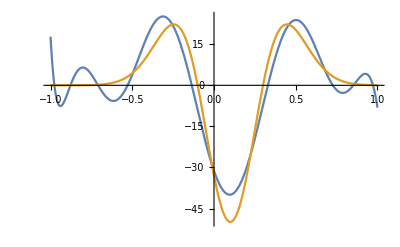

```mathematica
q=Table[NIntegrate[qFunc[x]BasisFunc[n][x],{x,-1,1}],{n,0,BasisMax}];
Plot[{q.Table[BasisFunc[n][x],{n,0,BasisMax}],qFunc[x]},{x,-1,1},PlotRange->All]


(LegDerivative={ConstantArray[0,Max[BasisMax]+1]}~Join~Table[Normal[SparseArray[Band[l,1,-2]->Array[(2(l-2#)-1)&,Quotient [l,2]+1,0],{Max[BasisMax]+1}]],{l,1,Max[BasisMax]}])//MatrixForm;
(LegDerivative=Transpose[MapIndexed[#1Sqrt[(2#2[[1]]-1)/(2#2[[2]]-1)]&,LegDerivative,{2}]])//MatrixForm;

MatrixPower[Transpose[LegDerivative],2].q
Plot[{%.Table[BasisFunc[n][x],{n,0,BasisMax}],Evaluate[D[qFunc[x],{x,2}]]},{x,-1,1}]
```

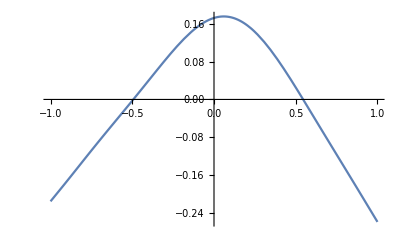

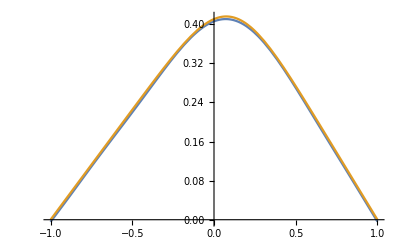

```mathematica
T=-Inverse[MatrixPower[LegDerivative,2][[;;-3,3;;]]].(q[[;;-3]]);
Plot[{T.Table[BasisFunc[n][x],{n,2,BasisMax}]},{x,-1,1},PlotRange->All]

T={0.33,0.018}~Join~T;

sol=y/.NDSolve[{y''[x]==-qFunc[x],y[-1]==0,y[1]==0},y,x][[1]];
Plot[{T.Table[BasisFunc[n][x],{n,0,BasisMax}],sol[x]},{x,-1,1},PlotRange->All]
```

Домашнее задание
1) Найти решение семинарской задачи с граничными условиями y[-1]=a, y’[-1]=b.
2) Решить уравнение Пуассона на отрезке от -1 до 1 методом Релея-Ритца (минимизация функционала). Базисные функции выбрать на свое усмотрение:
	Прочитать про слабую формулировку граничных условий, естественные и необходимые граничные условия. Например глава 5.3.1 Pei-bai Zhou Numerical Analysis of Electromagnetic Fields. Какое граничное условие “зашито” в метод Рэлея-Ритца? Каким образом можно изменять граничные условия? Уметь доказать это на бумаге.
	Метод Релея-Ритца. Выразить функционал через вектор столбец коэффициентов искомой функции. Создать облать в которой будут меняться искомые коэффициенты. Она будет размерности BasisMax+1. Возможно пригодится оператор Cuboid. Найти минимум функционала в созданной области. Возможно будет полезен оператор NMinimize. Построить функцию по найденным коэффициентам.
	Какие граничные условия Неймана имеют физический смысл? Условие самосогласованности, ее физическая интерпретация
	Изменить функционал так, чтобы находилась функция с граничными условиями Неймана y’[-1]=a, y’[1]=b. Использовать слабую формулировку
	Найти решение, удовлетворяющее граничным условиям Дирихле y[-1]=a, y[1]=b. Возможно для этого придется повнимательней просмотреть хелп оператора NMinimize